# Idear: Use best-fit n_m and R_B from J-V fits to see what happens to density at FAST altitudes

## Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

```mathematica
peakEBoundsIndShift=0;
```

```mathematica
peakEBoundsIndShift=False;
```

#### peakEBounds shift selection and string setup

```mathematica
peakEBoundsSuff="";If[ToString[Head[peakEBoundsIndShift]]=="Integer",peakEBoundsSuff=ToString@StringForm["-peakE_indShift_eq_`1`",peakEBoundsIndShift]];
```

#### From Orbit 1612 J-V fits, fixed temperature

```mathematica
RBFASTtoIonos=3.95241; (*As attested by MEDIAN() stuff in RESTORELASTKAPPA for orbit 1612*)
```

Maxwellian, then kappa

```mathematica
{I2JVFixT,I2JVNoFixT}={
Association["Maxwellian"->{140,0.79,15,∞},"Kappa"->{180,0.61,31.2,1.85}],
Association["Maxwellian"->{75,0.7,17.5,∞},"Kappa"->{76,0.70,17.9,34.9}]
};
```

```mathematica
interval=2;
```

```mathematica
fitType = "Maxwellian";
```

```mathematica
fitType = "Kappa";
```

#### These are derived using peakE_bounds_indShift=[0,0]

```mathematica
If[peakEBoundsIndShift==0,
Switch[interval,
	1,
		,
	2,
		{Tm,nm,RB,kappa} = I2JVFixT[fitType]]];
```

#### These are derived using NO peakE_bounds _indShift

```mathematica
If[(ToString@Head[peakEBoundsIndShift])≠ "Integer",
Switch[interval,
1,
	,
2,
	{Tm,nm,RB,kappa} = I2JVFixT[fitType]]]
```

{180,0.61,31.2,1.85}

### And the interval …

```mathematica
Print[ToString@StringForm["spectraAvgItvl: `1`",spectraAverageInterval]];
Print[ToString@StringForm["peakEBoundsIndShift: `1`",peakEBoundsIndShift]];
```

spectraAvgItvl: 2

```mathematica
RBSourceToFAST=RB/RBFASTtoIonos
```

7.89392

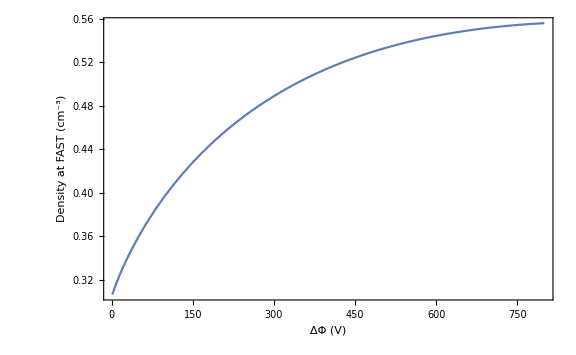

```mathematica
Plot[nm*LKMwellDensFac[pot/Tm,RBSourceToFAST],{pot,1,800},Frame->True,FrameStyle->(FontSize->16),ImageSize->Large,FrameLabel->{"ΔΦ (V)","Density at FAST (cm^-3)"}]
```

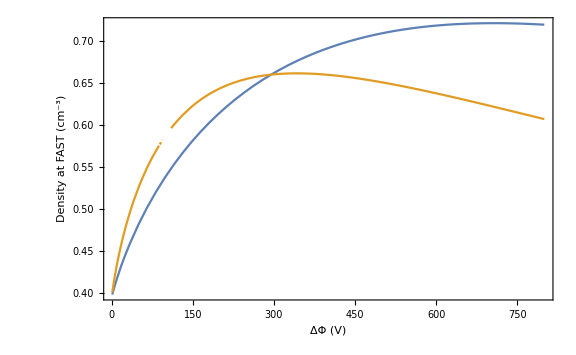

```mathematica
Plot[{nm*LKMwellDensFac[pot/Tm,RBSourceToFAST],nm*LKKappaDensFac[pot/180,RBSourceToFAST,2.11]},{pot,1,800},Frame->True,FrameStyle->(FontSize->16),ImageSize->Large,FrameLabel->{"ΔΦ (V)","Density at FAST (cm^-3)"}]
```

```mathematica
Manipulate[Plot[{nm*LKMwellDensFac[pot/T,RBAtFAST],nm*LKKappaDensFac[pot/T,RBAtFAST,2.4]},{pot,1,800},Frame->True,FrameStyle->(FontSize->16),ImageSize->Large,FrameLabel->{"ΔΦ (V)","Density at FAST (cm^-3)"}],{{RBAtFAST,RBSourceToFAST},2,50},{{T,Tm},10,500}]
```

```mathematica
(*Switch[interval,
1,
	Switch[fitType,
	"Maxwellian",
		{Tm,nm,RB,kappa}={140,0.79,15,∞};
	"Kappa",
		{Tm,nm,RB,kappa}={180,0.61,31.2,1.85};
],
2,
	Switch[fitType,
	"Maxwellian",
		{Tm,nm,RB,kappa}={140,0.79,15,∞};
	"Kappa",
		{Tm,nm,RB,kappa}={180,0.61,31.2,1.85};
]
]*)
```